```mathematica
vmax=5;
p=0.9;
rho=Round[(1-p)/(vmax+1-2*p),0.001];
dmin=Round[rho/2,0.001];
dmax=Round[rho*1.5,0.001];
dd=Round[(dmax-dmin)/10,0.001];
rho " :Transition density!!!"
dmin ": Min density"
dmax ": Max density"
dd ": density step"
"List of simulated values:"
For[i=-1,i<10,i++;
Print[dmin+i*dd]
]
```

0.024  :Transition density!!!

0.012 : Min density

0.036 : Max density

0.002 : density step

List of simulated values:

0.012

0.014

0.016

0.018

0.02

0.022

0.024

0.026

0.028

0.03

0.032

0.9

16384. = L

229 = N

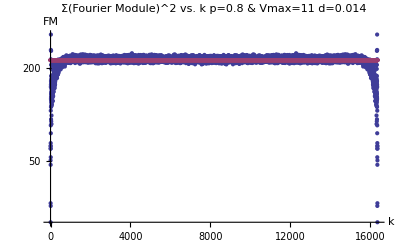

225.813 = N*(L-N)/(L-1)

231.238 = Mean of o.7 largest values

3.6995×10^6 = Sum of All L-1 Valus

3.6995×10^6 = N*(L-N)

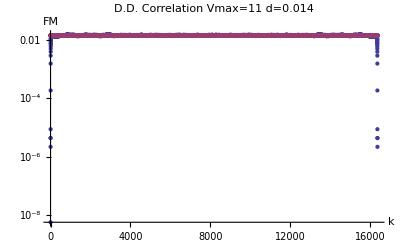

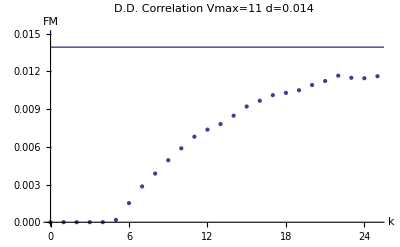

0.0139169 = (N-1)/(L-1)

0.0139938 = Mean of o.9 largest values

0.0139169 = Mean of all L-1 values

0.000536548 = STDV of all L-1 values

0.0385538 = STDV/Mean

228. = Sum of All L Valus

228 = N-1

Values lesser than 2/3*(N-1)/(L-1):

{0,5.81033×10^-9}

{1,4.36525×10^-6}

{2,2.18593×10^-6}

{3,4.35861×10^-6}

{4,8.74118×10^-6}

{5,0.000183398}

{6,0.00151964}

{7,0.00284498}

{8,0.00386899}

{9,0.00493013}

{10,0.00587555}

{11,0.00679913}

{12,0.00736463}

{13,0.00780347}

{14,0.0084738}

{15,0.00919867}

```mathematica
d="0.014";
p="0.9"
n=16384.000;
a="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax5/short/fourier.1d.averaged.d";
b=".p"<>p<>".v5.txt";
g=".p"<>p<>".v5.txt";
c=a<>d<>b;
e="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax5/short/ddensitycorrelation.d";
f=e<>d<>g;
j=StringToStream[d];
o= Read[j,Number];
m=Floor[o*16384];
n "= L"
m  "= N  "
bitF=ReadList[c,{Number,Number}];
bitf2=bitF[[All,2]];
randomf=Table[{i,(n-m)*m/(n-1)},{i,0,16383}];
ListLogPlot[{bitF,randomf},PlotLabel->"Σ(Fourier Module)^2 vs. k  p=0.8 & Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
(n-m)*m/(n-1) "= N*(L-N)/(L-1)"
TrimmedMean[bitf2,{0.3,0}] "= Mean of o.7 largest values"
summ=Sum[bitf2[[i]],{i,1,n-1} ];
N[summ] "= Sum of All L-1 Valus"
m*(n-m) "= N*(L-N)"
Δ=summ-m*(n-m);
density=ReadList[f,{Number,Number}];
density2=density[[All,2]];
prand=(m-1)/(n-1);
random=Table[{i,prand},{i,0,16383}];
ListLogPlot[{density,random},PlotLabel->"D.D. Correlation Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
pic1=ListPlot[density,PlotLabel->"D.D. Correlation Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->{{0,25},Full}];
pic2=ListLinePlot[random];
Show[pic1,pic2]
prand  "= (N-1)/(L-1)"
TrimmedMean[density2,{0.1,0}] "= Mean of o.9 largest values"
mean=Mean[Delete[density2,1]] "= Mean of all L-1 values"
stdv=StandardDeviation[Delete[density2,1]]  "= STDV of all L-1 values"
StandardDeviation[Delete[density2,1]]/Mean[Delete[density2,1]] "= STDV/Mean"
summ2=Sum[density2[[i]],{i,1,n} ];
N[summ2] "= Sum of All L Valus"
m2=m-1;  
m2 "= N-1"
"Values lesser than 2/3*(N-1)/(L-1):"
For[i=0,i<50,i++,
If[density2[[i]]<2*prand/3,
Print[{i-1,density2[[i]]}]
]
]
```

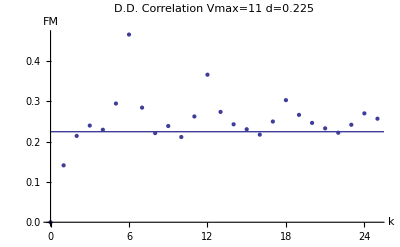

0.224928 = (N-1)/(L-1)

0.225052 = Mean of o.9 largest values

0.224928 = Mean of all L-1 values

0.00381096 = STDV of all L-1 values

0.016943 = STDV/Mean

3685. = Sum of All L Valus

3685 = N-1

Values lesser than 2/3*(N-1)/(L-1):

{0,-1.33463×10^-8}

{1,0.141331}

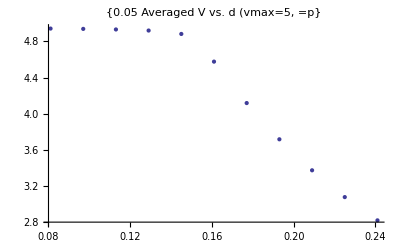

```mathematica
kk="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax5/short/v-p"<>p<>".txt";
vel=ReadList[kk,{Number,Number}];
ListPlot[vel,PlotLabel->{"Averaged V vs. d (vmax=5," p "=p"}]
```